```mathematica
mdwout = "/Volumes/homes/Code/cytomod/shila/semiflexible/out/network/";
mdwlcl="/home/simonfreedman/scratch-midway/cytomod/out/pl/";
mdwhm="/home/simonfreedman/Code/cytomod/shila/semiflexible/out/pl/";
```

```mathematica
ParticleTimeSeries[d_,n_]:=
Module[
{dir=d, name=n},
file=dir<>"/txt_stack/"<>name<>".txt";
particles=Import[file,"Table"];
(*Print["Finished importing "<>file];*)
timestamps = Position[particles,"t"][[All,1]];
particlesT=Table[particles[[timestamps[[i]]+1;;timestamps[[i+1]]-1]],{i,Length[timestamps]-1}];
particlesT=Append[particlesT, particles[[timestamps[[-1]]+1;;]]];
nparticles=Length[particlesT[[1]]];
dt=particles[[timestamps[[2]],3]]-particles[[timestamps[[1]],3]];
{nparticles, dt,particlesT}
];
```

```mathematica
End2End[d_,decorframe_]:=
Module[
{dir =d,
ndc=decorframe},
{np, dt,rt}=ParticleTimeSeries[d,"rods"];
{np,dt,lt}=ParticleTimeSeries[d,"links"];
nlinksT=Table[Length[l],{l,lt}];
fracture=Position[nlinksT,Except[Head[nlinksT]|nlinksT[[1]]],1,1];
fractureT=If[Length[fracture]>0, fracture[[1,1]],Length[rt]];
rt=rt[[1;;fractureT]];
ldTot=np*Sqrt[rt[[1,1,3]]^2+rt[[1,1,4]]^2];
e2es=Table[EuclideanDistance[rt[[t,1,1;;2]],rt[[t,-1,1;;2]]+rt[[t,-1,3;;4]]]/ldTot,{t,Ceiling[Length[rt]/2],Length[rt],ndc}];
e2es
];
```

```mathematica
seeds=Table[ToString[i],{i,800,847}];
basedir="nmon50_seed";
dirs=Table[mdwlcl<>basedir<>s,{s,seeds}];
```

```mathematica
e2es=Table[End2End[dr,1],{dr,dirs}];
```

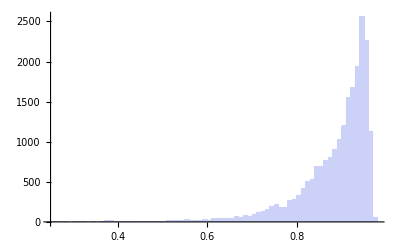

```mathematica
Histogram[Flatten[e2es]]
```

```mathematica
G[r_,k_,N_,T_]:=1/(2Pi N)2k/Sqrt[Pi]Sum[(2l-1)!!/(2^l*l!)1/(2k(1-r))^(5/4)Exp[-(l+1/4)^2/(2k(1-r))]*ParabolicCylinderD[3/2,2(l+1/4)/Sqrt[2k(1-r)]],{l,0,T}];
```

```mathematica
binnedE2Es=BinCounts[Flatten[e2es],{0,1,.01}];
```

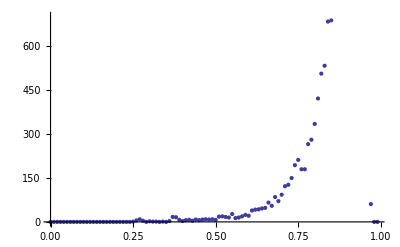

```mathematica
xaxis=Range[0,1,0.01];
hist=Table[{xaxis[[i]],binnedE2Es[[i]]},{i,Length[xaxis]-1}];
ListPlot[hist]
```

```mathematica
nlm=NonlinearModelFit[hist[[2;;-2]],G[r,k,n,1],{k,n},r];
```

NonlinearModelFit::nrlnum: The function value {0.000160466  - 0.000112759\ ⅈ, 0.00016269  - 0.000114113\ ⅈ, 0.000164969  - 0.000115497\ ⅈ, « 46 », -6.99959 - 0.0002498\ ⅈ, « 48 »} is not a list of real numbers with dimensions {98} at {k, n} = {-46.1817, -142.852}.

```mathematica
G[r,k,n,1]
```

1/(n π^(3/2))k ((ⅇ^(-1/(32 k (1-r))) ParabolicCylinderD[3/2,1/(2 √2 √(k (1-r)))])/(2 2^(1/4) (k (1-r))^(5/4))+(ⅇ^(-25/(32 k (1-r))) ParabolicCylinderD[3/2,5/(2 √2 √(k (1-r)))])/(4 2^(1/4) (k (1-r))^(5/4)))

```mathematica
nlm=NonlinearModelFit[hist[[2;;-2]],1/(n π^(3/2))k ((ⅇ^(-1/(32 k (1-r))) ParabolicCylinderD[3/2,1/(2 √2 √(k (1-r)))])/(2 2^(1/4) (k (1-r))^(5/4))),{{k,0.25},{n,1/5000}},r];
```

```mathematica
nlm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
k | 0.521691 | 0.0177553 | 29.3823 | 8.84713×10^-50
n | 0.000604643 | 0.0000224462 | 26.9374 | 1.51624×10^-46

```mathematica
Needs["PlotLegends`"]
```

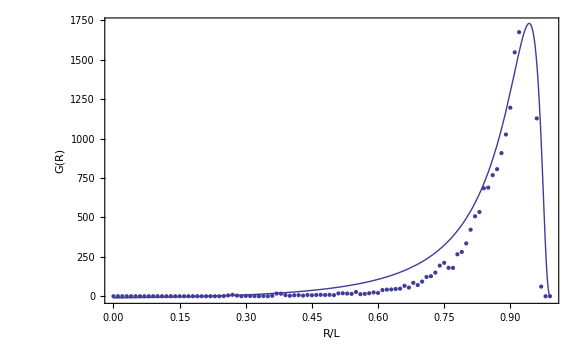

```mathematica
Show[Plot[Normal[nlm],{r,0,0.99}],ListPlot[hist],Frame->True, FrameLabel->{"R/L","G(R)","Radial Distribution Function of \nEnd to End Filament Distance"},BaseStyle->{FontSize->14}]
```

```mathematica
seeds=Table[ToString[i],{i,900,947}];
basedir="nmon50_seed";
dirs=Table[mdwlcl<>basedir<>s,{s,seeds}];
```

```mathematica
e2es900=Table[End2End[dr,1],{dr,dirs}];
```

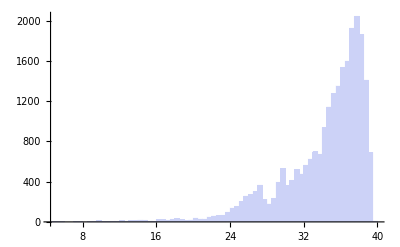

```mathematica
Histogram[Flatten[e2es900]]
```

```mathematica
binnedE2E900s=BinCounts[Flatten[e2es900],{0,1,.01}];
```

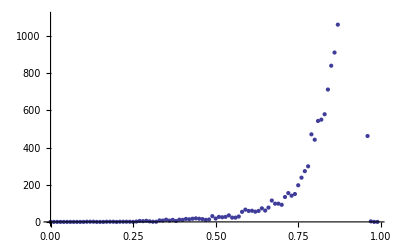

```mathematica
xaxis=Range[0,1,0.01];
hist=Table[{xaxis[[i]],binnedE2E900s[[i]]},{i,Length[xaxis]-1}];
ListPlot[hist]
```

```mathematica
nlm=NonlinearModelFit[hist[[2;;-2]],G[r,k,n,1],{{k,0.25},{n,1/2000}},r];
```

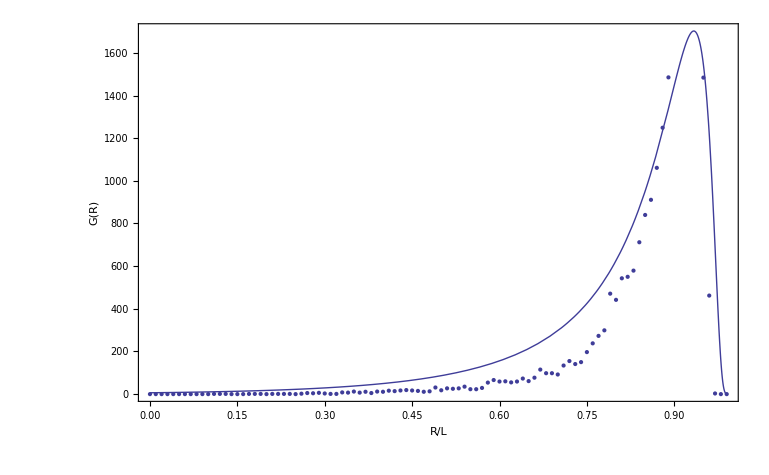

```mathematica
Show[Plot[Normal[nlm],{r,0,0.99}],ListPlot[hist],Frame->True, FrameLabel->{"R/L","G(R)","Radial Distribution Function of \nEnd to End Filament Distance"},BaseStyle->{FontSize->14}]
```

```mathematica
nlm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
k | 0.449275 | 0.0155261 | 28.9367 | 3.31148×10^-49
n | 0.000529239 | 0.0000198774 | 26.6252 | 4.07405×10^-46

```mathematica
seeds=Table[ToString[i],{i,1100,1147}];
basedir="nmon50_seed";
dirs=Table[mdwlcl<>basedir<>s,{s,seeds}];
```

```mathematica
e2es1100=Table[End2End[dr,1],{dr,dirs}];
```

```mathematica
binnedE2E1100s=BinCounts[Flatten[e2es1100],{0,1,.01}];
```

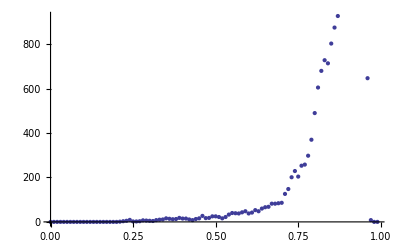

```mathematica
xaxis=Range[0,1,0.01];
hist=Table[{xaxis[[i]],binnedE2E1100s[[i]]},{i,Length[xaxis]-1}];
ListPlot[hist]
```

```mathematica
nlm=NonlinearModelFit[hist[[2;;-2]],G[r,k,n,1],{{k,0.25},{n,1/2000}},r];
```

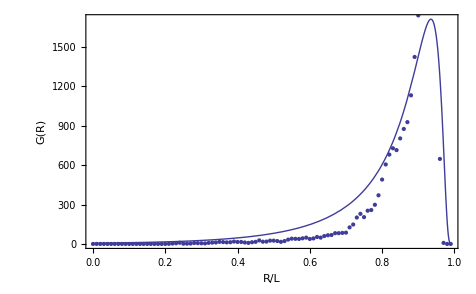

```mathematica
Show[Plot[Normal[nlm],{r,0,0.99}],ListPlot[hist],Frame->True, FrameLabel->{"R/L","G(R)","Radial Distribution Function of \nEnd to End Filament Distance"},BaseStyle->{FontSize->14}]
```

```mathematica
nlm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
k | 0.460449 | 0.0141106 | 32.6314 | 9.30126×10^-54
n | 0.000539901 | 0.0000179821 | 30.0243 | 1.3589×10^-50

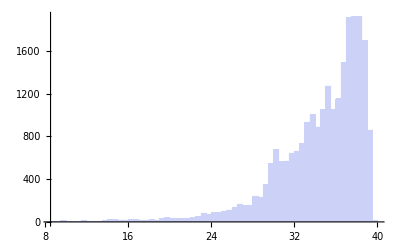

```mathematica
Histogram[Flatten[e2es1100]]
```

```mathematica
seeds=Table[ToString[i],{i,1000,1047}];
basedir="nmon50_seed";
dirs=Table[mdwlcl<>basedir<>s,{s,seeds}];
```

```mathematica
e2es1000=Table[End2End[dr,1],{dr,dirs}];
```

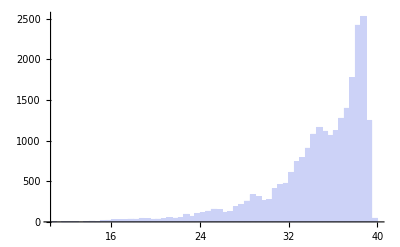

```mathematica
Histogram[Flatten[e2es1000]]
```